```mathematica
Needs["MaTeX`"]
```

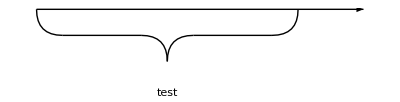

```mathematica
hbrace[p1_,p2_,h_,label_]:=Module[{m,c1,c2,c3,c4,t1,t2,t4},
m=1/2(p1+p2)+{0,h};
c1=p1+1/2{Abs[h],h};
t1=p1+1/2{0,h};
c2=m+1/2{-Abs[h],-h};
t2=m+1/2{0,-h};
c3=m+1/2{Abs[h],-h};
c4=p2+1/2{-Abs[h],h};
t4=p2+1/2{0,h};
{
BezierCurve[{p1,t1,c1}],
Line[{c1,c2}],
BezierCurve[{c2,t2,m}],
BezierCurve[{m,t2,c3}],
Line[{c3,c4}],
BezierCurve[{c4,t4,p2}],
Inset[label,m+0.6{0,h}]
}]
Graphics[{
Arrow[{{0,0},{2.5,0}}],
hbrace[{0,0},{2,0},-0.4,"test"]
}]
```

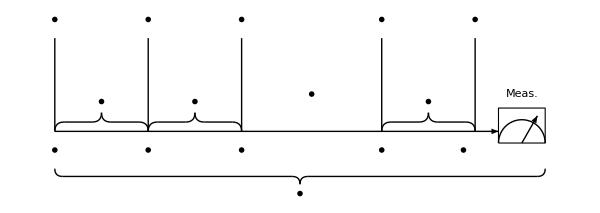

```mathematica
p=Module[{op=Magnification->1.5,voff={0,0.4}},
Graphics[
{Arrow[{{0,0},{9.5,0}}],
Line[{{0,0},{0,2}}],
Line[{{2,0},{2,2}}],
Line[{{4,0},{4,2}}],
Line[{{7,0},{7,2}}],
Line[{{9,0},{9,2}}],
hbrace[{0,0},{2,0},0.4,MaTeX["\\mathcal{U}_{\\mathrm{I}}(t_1,t_0)",op]],
hbrace[{2,0},{4,0},0.4,MaTeX["\\mathcal{U}_{\\mathrm{I}}(t_2,t_1)",op]],
hbrace[{7,0},{9,0},0.4,MaTeX["\\mathcal{U}_{\\mathrm{I}}(t_m,t_{m-1})",op]],
Inset[MaTeX["\\mathcal{G}_0",op],{0,2}+voff],
Inset[MaTeX["\\mathcal{G}_1",op],{2,2}+voff],
Inset[MaTeX["\\mathcal{G}_2",op],{4,2}+voff],
Inset[MaTeX["\\mathcal{G}_{m-1}",op],{7,2}+voff],
Inset[MaTeX["\\mathcal{G}_{m}",op],{9,2}+voff],
Inset[MaTeX["t_0",op],{0,0}-voff],
Inset[MaTeX["t_1",op],{2,0}-voff],
Inset[MaTeX["t_2",op],{4,0}-voff],
Inset[MaTeX["t_{m-1}",op],{7,0}-voff],
Inset[MaTeX["t_m \\equiv T",op],{8.75,0}-voff],
Inset[MaTeX["\\cdots",op],{5.5,0.8}],
{
FaceForm[],
EdgeForm[{Black}],
Rectangle[{9.5,-1/4},{10.5,1/2}],
Circle[{10,-1/4},0.5,{0,Pi}],
Arrowheads[0.03],
Arrow[{{10,-1/4},{10+1/3,1/3}}],
Inset[Style["Meas.",op,FontFamily->"CMU Serif"],{10,0.8}]
},
hbrace[{0,-0.8},{10.5,-0.8},-1/3,MaTeX["\\mathcal{S}_m",op]]
},ImageSize->600]]
```

```mathematica
p=Module[{op=Magnification->1.5,voff={0,0.4}},
Graphics[
{Arrow[{{0,0},{9.5,0}}],
Line[{{0,0},{0,2}}],
Line[{{2,0},{2,2}}],
Line[{{4,0},{4,2}}],
Line[{{7,0},{7,2}}],
Line[{{9,0},{9,2}}],
hbrace[{0,0},{2,0},0.4,MaTeX["\\mathcal{U}_{\\mathrm{I}}(t_1,t_0)",op]],
hbrace[{2,0},{4,0},0.4,MaTeX["\\mathcal{U}_{\\mathrm{I}}(t_2,t_1)",op]],
hbrace[{7,0},{9,0},0.4,MaTeX["\\mathcal{U}_{\\mathrm{I}}(t_m,t_{m-1})",op]],
Inset[MaTeX["\\mathcal{G}_0",op],{0,2}+voff],
Inset[MaTeX["\\mathcal{G}_1",op],{2,2}+voff],
Inset[MaTeX["\\mathcal{G}_2",op],{4,2}+voff],
Inset[MaTeX["\\mathcal{G}_{m-1}",op],{7,2}+voff],
Inset[MaTeX["\\mathcal{G}_{m}",op],{9,2}+voff],
Inset[MaTeX["t_0",op],{0,0}-voff],
Inset[MaTeX["t_1",op],{2,0}-voff],
Inset[MaTeX["t_2",op],{4,0}-voff],
Inset[MaTeX["t_{m-1}",op],{7,0}-voff],
Inset[MaTeX["t_m \\equiv T",op],{8.75,0}-voff],
Inset[MaTeX["\\cdots",op],{5.5,0.8}],
{
FaceForm[],
EdgeForm[{Black}],
Rectangle[{9.5,-1/4},{10.5,1/2}],
Circle[{10,-1/4},0.5,{0,Pi}],
Arrowheads[0.03],
Arrow[{{10,-1/4},{10+1/3,1/3}}],
Inset[Style["Meas.",op,FontFamily->"CMU Serif"],{10,0.8}]
},
hbrace[{0,-0.8},{10.5,-0.8},-1/3,MaTeX["\\mathcal{S}_m",op]]
},ImageSize->600]]
```

-Graphics-

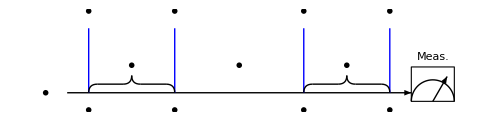

```mathematica
p=Module[{ op=Magnification->1.5,
doff=2,
hoff=1.5,
voff=0.4,
p0,d,h,v},

p0={0,0};
d={doff,0};
h={0,hoff};
v={0,voff};
Graphics[
{Arrow[{{-0.5,0},3.75d}],
Inset[MaTeX["|\\psi_0\\rangle",op],{-1,0}],
{Thick,Blue,Line[{p0,h}],
Line[{d,d+h}],Line[{2.5d,2.5d+h}],
Line[{3.5d,3.5d+h}]
},
Inset[MaTeX["\\mathcal{G}_0",op],h+v],
Inset[MaTeX["t_0",op],-v],

Inset[MaTeX["\\mathcal{G}_1",op],d+h+v],
Inset[MaTeX["t_1",op],d-v],

Inset[MaTeX["\\mathcal{G}_{m-1}",op],2.5d+v+h],
Inset[MaTeX["t_{m-1}",op],2.5d-v],

Inset[MaTeX["\\mathcal{G}_{m}",op],3.5d+v+h],
Inset[MaTeX["t_m",op],3.5d-v],
Inset[MaTeX["\\cdots",op],(3.5/2)d+1.6v],
hbrace[p0,d,voff,MaTeX["\\mathcal{U}_{\\mathrm{f}}",op]],
hbrace[2.5d,3.5d,voff,MaTeX["\\mathcal{U}_{\\mathrm{f}}",op]],
Module[{boxpos1=3.75d-0.5v,blen=0.5doff,bh=2voff,boxpos2,bm},{
boxpos2=boxpos1+{blen,bh};
bm=boxpos1+0.5{blen,0};
FaceForm[],
EdgeForm[{Black}],
Rectangle[boxpos1,boxpos2],
Circle[bm,0.5blen,{0,Pi}],
Arrowheads[0.03],
Arrow[{bm,bm+2/3blen{Cos[#],Sin[#]}&[π/3]}],
Inset[Style["Meas.",op,FontFamily->"CMU Serif"],bm+{0,bh+0.6voff}]
}]
},ImageSize->500]]
```

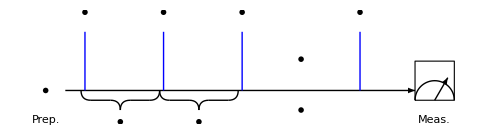

```mathematica
p=Module[{ op=Magnification->1.5,
doff=2,
hoff=1.5,
voff=0.5,
xeps=0.1,
p0,d,h,v,eps},

p0={0,0};
d={doff,0};
h={0,hoff};
v={0,voff};
eps={xeps,0};
Graphics[
{Arrow[{{-0.5,0},4.2d}],
Inset[MaTeX["|\\psi_0\\rangle",op],{-1,0}],
Inset[Style["Prep.",op,FontFamily->"CMU Serif"],{-1,-1.5voff}],
{Thick,Blue,Line[{p0,h}],
Line[{d,d+h}],Line[{2d,2d+h}],
Line[{3.5d,3.5d+h}]
},
Inset[MaTeX["\\mathcal{G}_0",op],h+v],


Inset[MaTeX["\\mathcal{G}_2",op],2d+h+v],


Inset[MaTeX["\\mathcal{G}_1",op],d+h+v],


Inset[MaTeX["\\mathcal{G}_{m}",op],3.5d+v+h],

Inset[MaTeX["\\cdots",op],(1+3.5/2)d-v],
Inset[MaTeX["\\cdots",op],(1+3.5/2)d+1.6v],
hbrace[p0-eps,d-eps,-voff,MaTeX["\\widetilde{\\mathcal{G}}_0",op]],
hbrace[d-eps,2d-eps,-voff,MaTeX["\\widetilde{\\mathcal{G}}_{1}",op]],
Module[{boxpos1=4.2d-0.5v,blen=0.5doff,bh=2voff,boxpos2,bm},{
boxpos2=boxpos1+{blen,bh};
bm=boxpos1+0.5{blen,0};
FaceForm[],
EdgeForm[{Black}],
Rectangle[boxpos1,boxpos2],
Circle[bm,0.5blen,{0,Pi}],
Arrowheads[0.03],
Arrow[{bm,bm+2/3blen{Cos[#],Sin[#]}&[π/3]}],
Inset[Style["Meas.",op,FontFamily->"CMU Serif"],{bm[[1]],-1.5voff}]
}]
},ImageSize->500]]
```

```mathematica
Export[NotebookDirectory[]<>"img/pulses-simple.pdf",p]
```

/Users/jiaan/Desktop/thesis/img/pulses-simple.pdf

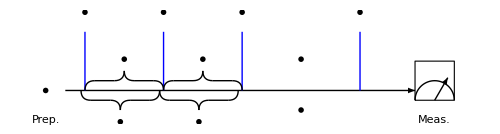

```mathematica
p2=Module[{ op=Magnification->1.5,
doff=2,
hoff=1.5,
voff=0.5,
xeps=0.1,
p0,d,h,v,eps},

p0={0,0};
d={doff,0};
h={0,hoff};
v={0,voff};
eps={xeps,0};
Graphics[
{Arrow[{{-0.5,0},4.2d}],
Inset[MaTeX["|\\psi_0\\rangle",op],{-1,0}],
Inset[Style["Prep.",op,FontFamily->"CMU Serif"],{-1,-1.5voff}],
{Thick,Blue,Line[{p0,h}],
Line[{d,d+h}],Line[{2d,2d+h}],
Line[{3.5d,3.5d+h}]
},
Inset[MaTeX["\\mathcal{G}_0",op],h+v],

hbrace[p0,d,voff,MaTeX["\\mathcal{U}_{\\mathrm{f}}(t_1,t_0)",op]],
hbrace[d,2d,voff,MaTeX["\\mathcal{U}_{\\mathrm{f}}(t_2,t_1)",op]],
Inset[MaTeX["\\mathcal{G}_2",op],2d+h+v],


Inset[MaTeX["\\mathcal{G}_1",op],d+h+v],


Inset[MaTeX["\\mathcal{G}_{m}",op],3.5d+v+h],

Inset[MaTeX["\\cdots",op],(1+3.5/2)d-v],
Inset[MaTeX["\\cdots",op],(1+3.5/2)d+1.6v],
hbrace[p0-eps,d-eps,-voff,MaTeX["\\widetilde{\\mathcal{G}}_0",op]],
hbrace[d-eps,2d-eps,-voff,MaTeX["\\widetilde{\\mathcal{G}}_{1}",op]],
Module[{boxpos1=4.2d-0.5v,blen=0.5doff,bh=2voff,boxpos2,bm},{
boxpos2=boxpos1+{blen,bh};
bm=boxpos1+0.5{blen,0};
FaceForm[],
EdgeForm[{Black}],
Rectangle[boxpos1,boxpos2],
Circle[bm,0.5blen,{0,Pi}],
Arrowheads[0.03],
Arrow[{bm,bm+2/3blen{Cos[#],Sin[#]}&[π/3]}],
Inset[Style["Meas.",op,FontFamily->"CMU Serif"],{bm[[1]],-1.5voff}]
}]
},ImageSize->500]]
```

```mathematica
Export[NotebookDirectory[]<>"img/pulses-simple2.pdf",p2]
```

/Users/jiaan/Desktop/thesis/img/pulses-simple2.pdf

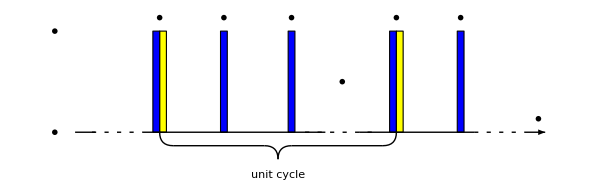

```mathematica
p3=Module[{ op=Magnification->1.5,
tmax=5,
tmin=-1.5,
tdash=0.75,
dt={1,0},
dpluse=0.05,
hpluse=1.5,
hoff=0.3,
voff=0.2,
xeps=0.1,
p0,h,v,p,eps},

p0={0,0};
h={0,hpluse};
p={dpluse,0};
v={0,voff};
eps={xeps,0};

Graphics[{
{EdgeForm[Black],FaceForm[Blue],
Rectangle[-p,p+h],
Rectangle[-p+dt,p+h+dt],
Rectangle[-p+2dt,p+h+2dt],
Rectangle[-p+3.5dt,p+h+3.5dt],
Rectangle[-p+4.5dt,p+h+4.5dt],
FaceForm[Yellow],
Rectangle[p,3p+h],
Rectangle[p+3.5dt,3p+h+3.5dt]
},
Text[MaTeX["P_K\ Q_i",op],h+v+p],
Text[MaTeX["P_1",op],dt+h+v],
Text[MaTeX["P_2",op],2dt+h+v],
Text[MaTeX["P_K\ Q_{i+1}",op],3.5dt+v+h+p],
Text[MaTeX["P_1",op],4.5dt+h+v],

Line[{{tmin+hoff,0},{tmin+2hoff,0}}],
Line[{{-voff,0},{2.5,0}}],
Line[{{3,0},{4.5+voff,0}}],
Arrowheads[0.025],
Arrow[{{4.5+tdash+voff,0},{4.5+tdash+2.5voff,0}}],

{
Dashing[{0.005,0.01}],
Line[{{-tdash-voff,0},{-voff,0}}],
Line[{{2+voff,0},{3.5-voff,0}}],
Line[{{4.5+voff,0},{4.5+tdash+voff,0}}]
},

Text[MaTeX["|\\psi_0\\rangle",op],{tmin,0}],

Text[MaTeX["H_{\\mathrm{ctrl}}",op],{tmin,hpluse}],
Text[MaTeX["t",op],{4.5+tdash+2voff,voff}],


Inset[MaTeX["\\cdots",op],(1+3.5/2)dt+0.5h],
hbrace[{dpluse,0},{dpluse,0}+3.5dt,-2voff,Style["unit cycle",op]]
},ImageSize->600]]
```